```mathematica
OffD1n[n_,p1_,p2_]:=Piecewise[{{-16Sqrt[n(n+1)](n+1/2) (ⅇ^(ⅈ p1 Log[(n+1)/(n+1/2)])ⅇ^(ⅈ p2 Log[(n+1/2)/n])+ⅇ^(ⅈ p2 Log[(n+1)/(n+1/2)])ⅇ^(ⅈ p1 Log[(n+1/2)/n])+ⅇ^(ⅈ p1 Log[(n+1)/(n+1/2)])+ⅇ^(ⅈ p2 Log[(n+1)/(n+1/2)])+ⅇ^(ⅈ p2 Log[(n+1/2)/n])+ⅇ^(ⅈ p1 Log[(n+1/2)/n])),n≠0},{0,n==0}},0];
OffD2n[n_,p1_,p2_]:=Piecewise[{{-16 Sqrt[n(n-1)](n-1/2)(ⅇ^(ⅈ p1 Log[(n-1)/(n-1/2)])ⅇ^(ⅈ p2 Log[(n-1/2)/n])+ⅇ^(ⅈ p2 Log[(n-1)/(n-1/2)])ⅇ^(ⅈ p1 Log[(n-1/2)/n])+ⅇ^(ⅈ p1 Log[(n-1)/(n-1/2)])+ⅇ^(ⅈ p2 Log[(n-1)/(n-1/2)])+ⅇ^(ⅈ p2 Log[(n-1/2)/n])+ⅇ^(ⅈ p1 Log[(n-1/2)/n])),n≠0&&n≠1},{0,n==0},{0,n==1}},0]
Diagn[n_,m1_,m2_]:=Piecewise[{{16n (n+1/2)(ⅇ^(ⅈ m1 Log[n/(n+1/2)])ⅇ^(ⅈ m2 Log[(n+1/2)/n])+ⅇ^(ⅈ m2 Log[n/(n+1/2)])ⅇ^(ⅈ m1 Log[(n+1/2)/n])+ⅇ^(ⅈ m1 Log[n/(n+1/2)])+ⅇ^(ⅈ m2 Log[n/(n+1/2)])+ⅇ^(ⅈ m2 Log[(n+1/2)/n])+ⅇ^(ⅈ m1 Log[(n+1/2)/n]))+16n (n-1/2)(ⅇ^(ⅈ m1 Log[n/(n-1/2)])ⅇ^(ⅈ m2 Log[(n-1/2)/n])+ⅇ^(ⅈ m2 Log[n/(n-1/2)])ⅇ^(ⅈ m1 Log[(n-1/2)/n])+ⅇ^(ⅈ m1 Log[n/(n-1/2)])+ⅇ^(ⅈ m2 Log[n/(n-1/2)])+ⅇ^(ⅈ m2 Log[(n-1/2)/n])+ⅇ^(ⅈ m1 Log[(n-1/2)/n])),n≠0},{0,n==0}},0]
```

```mathematica
e=0;
T =5;
p1=5;
p2=5;
Clear[b,n]
b=RecurrenceTable[{OffD1n[n,p1,p2]a[n+1] + Diagn[n,p1,p2]a[n]+ OffD2n[n,p1,p2]a[n-1]==e a[n],a[0]==0,a[1]==1.},a, {n,1,T}];
```

```mathematica
Clear[psi]
T=1000;
e=ⅈ;
p1=4.;
p2=4.;
psi=Table[1,{i,1,T}];
psi[[1]]=1;
For[n=1,n≤T,n++,
	psi[[n+1]]=1/OffD1n[n,p1,p2](e psi[[n]]-Diagn[n,p1,p2]psi[[n]]-OffD2n[n,p1,p2] psi[[n-1]]);]
```

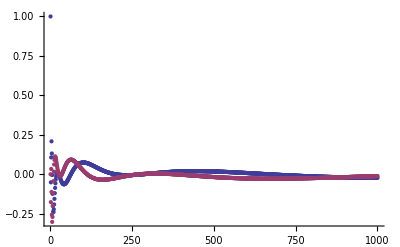

```mathematica
ListPlot[{Re[psi],Im[psi]}]
```

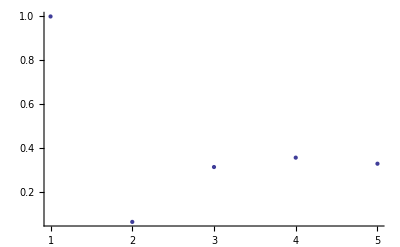

```mathematica
aa=ListPlot[Abs[b]]
```

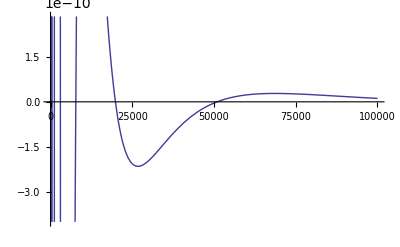

```mathematica
bb=Plot[Re[1/(√x)ⅇ^(ⅈ Log[x](-1/3 (p1+p2) + 1/6 √(3e/8 - 4(p1^2+p2^2-p1 p2))))],{x,1,100000}]
```